```mathematica
soln1=NDSolve[{
x1'[t]==-10 (x1[t]-y1[t]),
y1'[t]==60 x1[t]-y1[t]-x1[t]z1[t],
z1'[t]==-(8/3)z1[t]+x1[t] y1[t],
x1[0]==4,y1[0]==-5,z1[0]==20},
{x1,y1,z1},{t,0,100},MaxSteps->25000]
```

{{x1→InterpolatingFunction[{{0.,100.}},<>],y1→InterpolatingFunction[{{0.,100.}},<>],z1→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
plot=ParametricPlot3D[Evaluate[{x1[t],y1[t],z1[t]}/.soln1],{t,0,100},AxesLabel->{"x","y","z"},PlotPoints->1000,
PlotRange->{{-50,50},{-50,50},{0,100}}]
```

-Graphics3D-

```mathematica
x2[t_]:=x1[t]/.soln1[[1]]
```

```mathematica
soln2=NDSolve[{
y2'[t]==60 x2[t]-y2[t]-x2[t] z2[t],
z2'[t]==-(8/3)z2[t]+x2[t] y2[t],
y2[0]==0,z2[0]==25},
{y2,z2},{t,0,100},MaxSteps->25000]
```

{{y2→InterpolatingFunction[{{0.,100.}},<>],z2→InterpolatingFunction[{{0.,100.}},<>]}}

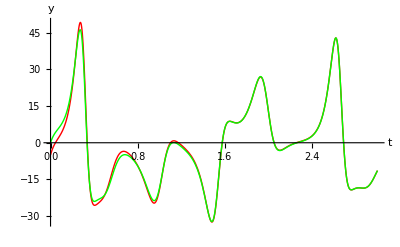

```mathematica
Plot[{(y1[t]/.soln1[[1]]),(y2[t]/.soln2[[1]])},{t,0,10},AxesLabel->{"t","y"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,1,0]}]
```

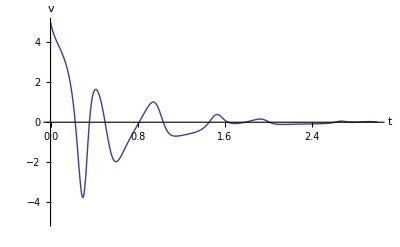

```mathematica
Plot[(y2[t]/.soln2[[1]])-(y1[t]/.soln1[[1]]),{t,0,3},AxesLabel->{"t","v"},PlotRange->{-5,5}]
```